```mathematica
SetDirectory[NotebookDirectory[]];
nn={
{"动画",RGBColor[0.5, 0.5, 1]},
{"番剧",RGBColor[0.5, 0.5, 1]},
{"国创",RGBColor[0.5, 0.5, 1]},
{"音乐",RGBColor[1, 1, 0]},
{"舞蹈",RGBColor[1, 0.5, 0]},
{"游戏",RGBColor[1, 0, 0]},
{"科技",RGBColor[0, 0.5, 1]},
{"生活",RGBColor[0, 0.5, 0]},
{"鬼畜",RGBColor[0.5, 1, 1]},
{"时尚",RGBColor[1, 0.5, 1]},
{"广告",RGBColor[1, 0.5, 1]},
{"娱乐",RGBColor[1, 0.5, 1]},
{"影视",RGBColor[1, 0.5, 1]},
{"放映厅",RGBColor[1, 0.5, 1]}
};
```

```mathematica
d=(Import["llc//"<>ToString@nn⟦#,1⟧<>".csv",CharacterEncoding-> "UTF-8"])&/@Range@Length@nn;
```

```mathematica
Export["totalview.csv",Table[
Join[{d⟦1,j,1⟧},Table[d⟦i,j,3⟧,{i,1,Length@nn}]]
,{j,2,Length[d⟦1⟧]}]]
```

totalview.csv

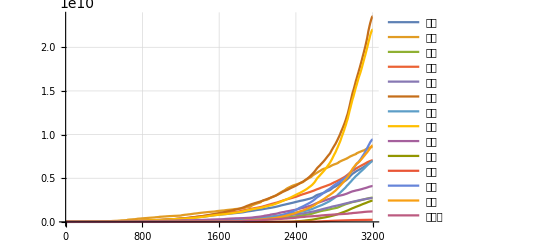

```mathematica
ListPlot[Table[{j,d⟦i,j,3⟧},{i,1,Length@nn},{j,2,Length[d⟦i⟧]}],PlotRange->All,PlotLegends->nn⟦All,1⟧,GridLines->Automatic,GridLinesStyle->Directive[Gray,Thin, Dashed],Joined->True]
```

```mathematica
SetOptions[BarChart,Frame->True,FrameStyle->Directive[Black,12],RotateLabel->True,FrameTicksStyle->16,BaseStyle->{FontSize->16},GridLinesStyle->Directive[Gray,Thin, Dashed]];
```

```mathematica
Manipulate[
BarChart[d⟦1;;Length@nn,u,-1⟧,ChartStyle->"DarkRainbow",ChartLabels->nn⟦All,1⟧,FrameLabel->{None,"总播放量"},GridLines->Automatic],
{u,1,3199}]
```

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

BarChart::ldata: Symbol[] 不是一个有效的数据集或者数据集列表.

General::stop: 在本次计算中，BarChart::ldata 的进一步输出将被抑制.

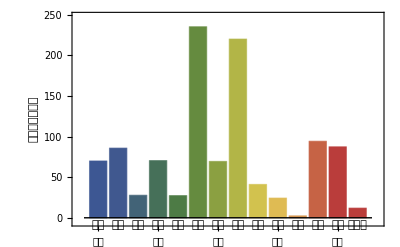

```mathematica
Table[d⟦i,-1,-1⟧/d⟦i,-1,-2⟧,{i,1,Length@nn}]/10^4//N
```

{0.781046,6.64054,3.85061,0.472466,1.22601,0.45577,0.774359,0.903275,3.34401,0.72714,0.32342,0.590784,0.896183,1.39875}

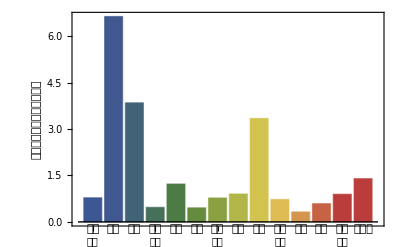

```mathematica
BarChart[%15,ChartStyle->"DarkRainbow",ChartLabels->nn⟦All,1⟧,Frame->Left,FrameLabel->{None,"每个视频平均播放量（万）"}]
```

```mathematica
Table[d⟦i,-1,-2⟧,{i,1,Length@nn}]/10^4//N
```

{89.6094,12.9266,7.2155,149.148,22.297,516.247,89.6643,243.697,12.2894,33.4367,7.4436,159.602,97.5688,8.5503}

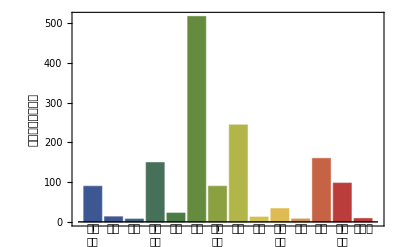

```mathematica
BarChart[%17,ChartStyle->"DarkRainbow",ChartLabels->nn⟦All,1⟧,Frame->Left,FrameLabel->{None,"现存稿件量（万）"}]
```

```mathematica
Manipulate[
BarChart[d⟦1;;Length@nn,u,-1⟧,ChartStyle->"DarkRainbow",ChartLabels->nn⟦All,1⟧,FrameLabel->{None,"总播放量"},GridLines->Automatic],
{u,1,3199}]
```

```mathematica
Manipulate[
Graphics3D[Flatten@Table[{Opacity[.75],
nn⟦i,2⟧,Cylinder[{{nn⟦i,3⟧,nn⟦i,4⟧,0},{nn⟦i,3⟧,nn⟦i,4⟧,If[d⟦i,u,2⟧>0,d⟦i,u,3⟧/d⟦i,u,2⟧/10,0]}},√d⟦i,u,2⟧]
},{i,1,Length@nn}],
FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},PlotRange->{{-10^3,1.5*10^4},{-3*10^3,9*10^3},{0,1.3*10^4}},Background->Black,Axes->True,Ticks->None,AxesLabel->{d⟦1,u,1⟧,"",""}],
{u,2,3199}]
```

Part::partw: {动画,RGBColor[0.5, 0.5, 1]} 的部分 3 不存在.

Part::partw: {动画,RGBColor[0.5, 0.5, 1]} 的部分 4 不存在.

Part::partw: {动画,RGBColor[0.5, 0.5, 1]} 的部分 3 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

```mathematica
nn={
{"动画",RGBColor[0.5, 0.5, 1],0,2000},
{"番剧",RGBColor[0.5, 0.5, 1],-500,4000},
{"国创",RGBColor[0.5, 0.5, 1],600,3500},
{"音乐",RGBColor[1, 1, 0],2300,-400},
{"舞蹈",RGBColor[1, 0.5, 0],3800,1500},
{"游戏",RGBColor[1, 0, 0],3000,6000},
{"科技",RGBColor[0, 0.5, 1],6000,0},
{"生活",RGBColor[0, 0.5, 0],8000,5000},
{"鬼畜",RGBColor[0.5, 1, 1],6000,8000},
{"时尚",RGBColor[1, 0.5, 1],9000,-1000},
{"广告",RGBColor[1, 0.5, 1],10000,-2000},
{"娱乐",RGBColor[1, 0.5, 1],10000,1000},
{"影视",RGBColor[1, 0.5, 1],12000,-1000},
{"放映厅",RGBColor[1, 0.5, 1],13000,0}
};
```